### Test Set

```mathematica
(*Define a helper function to create test function associations*)
CreateTestFunction[name_,def_,x0_]:=<|"Name"->name,"Definition"->def,"x0"->x0|>;

(*Create the test set with inline function definitions*)
CreateTestFunction[name_, def_, x0_] := <|"Name" -> name, "Definition" -> def, "x0" -> x0|>;
TestSet = {
	CreateTestFunction[
      "Extended Trigonometric Function",
      Function[x, Module[{n = Length[x]},
         Sum[
            ((n - Sum[Cos[x[[j]]], {j, n}]) + i (1 - Cos[x[[i]]]) - Sin[x[[i]]])^2,
            {i, n}
         ]
      ]],
      Function[n, Table[0.2, {n}]]
   ],
   CreateTestFunction[
      "Generalized Rosenbrock Function",
      Function[x, Module[{n = Length[x], c = 100.0},
         Sum[c (x[[i + 1]] - x[[i]]^2)^2 + (1.0 - x[[i]])^2, {i, n - 1}]
      ]],
      Function[n, Table[If[OddQ[i], -1.2, 1], {i, n}]]
   ],
   CreateTestFunction[
      "Extended Penalty Function",
      Function[x, Module[{n = Length[x]},
         Sum[(x[[i]] - 1)^2, {i, 1, n - 1}] + (Sum[x[[j]]^2, {j, 1, n}] - 0.25)^2
      ]],
      Function[n, Table[i, {i, n}]]
   ],
   CreateTestFunction[
      "Perturbed Quadratic Function",
      Function[x, Module[{n = Length[x]},
         Sum[i x[[i]]^2, {i, n}] + (1/100) (Sum[x[[i]], {i, n}])^2
      ]],
      Function[n, Table[0.5, {n}]]
   ],
   CreateTestFunction[
      "Generalized Tridiagonal 1 Function",
      Function[x, Module[{n = Length[x]},
         Sum[x[[i]]^2 + x[[i]] x[[i + 1]] - 4 x[[i + 1]]^2 + 3 x[[i + 1]], {i, 1, n - 1}]
      ]],
      Function[n, Table[2, {n}]]
   ],
   CreateTestFunction[
      "Generalized White & Holst Function",
      Function[x, Module[{n = Length[x], c = 100},
         Sum[c (x[[i + 1]] - x[[i]]^3)^2 + (1 - x[[i]])^2, {i, n - 1}]
      ]],
      Function[n, Table[If[OddQ[i], -1.2, 1], {i, n}]]
   ],
   CreateTestFunction[
      "Generalized PSC1 Function",
      Function[x, Module[{n = Length[x]},
         Sum[
            (x[[i]]^2 + x[[i + 1]]^2 + x[[i]] x[[i + 1]])^2 + Sin[x[[i]]]^2 + Cos[x[[i]]]^2,
            {i, n - 1}
         ]
      ]],
      Function[n, Table[If[OddQ[i], 3, 0.1], {i, n}]]
   ],
   CreateTestFunction[
      "Full Hessian FH1 Function",
      Function[x, Module[{n = Length[x]},
         (x[[1]] - 3)^2 + Sum[
            (x[[1]] - 3 - 2 (Sum[x[[j]], {j, i}])^2)^2,
            {i, 2, n}
         ]
      ]],
      Function[n, Table[0.01, {n}]]
   ],
   CreateTestFunction[
      "Full Hessian FH2 Function",
      Function[x, Module[{n = Length[x]},
         (x[[1]] - 5)^2 + Sum[
            (Sum[x[[j]], {j, i}] - 1)^2,
            {i, 2, n}
         ]
      ]],
      Function[n, Table[0.01, {n}]]
   ],
   CreateTestFunction[
      "Perturbed Quadratic Diagonal Function",
      Function[x, Module[{n = Length[x]},
         (Sum[x[[i]], {i, n}])^2 + Sum[(i/100) x[[i]]^2, {i, n}]
      ]],
      Function[n, Table[0.5, {n}]]
   ],
   CreateTestFunction[
      "Quadratic QF1 Function",
      Function[x, Module[{n = Length[x]},
         (1/2) Sum[i x[[i]]^2, {i, n}] - x[[n]]
      ]],
      Function[n, Table[1, {n}]]
   ],
   CreateTestFunction[
      "Extended Quadratic Penalty QP1 Function",
      Function[x, Module[{n = Length[x]},
         Sum[(x[[i]]^2 - 2)^2, {i, 1, n - 1}] + Sum[(x[[i]]^2 - 0.5)^2, {i, n}]
      ]],
      Function[n, Table[1, {n}]]
   ],
   CreateTestFunction[
	  "Extended Quadratic Penalty QP2 Function",
	  Function[x, Module[{n = Length[x]},
	     (Sum[x[[i]]^2, {i, 1, n}] - 100)^2 + 
	     Sum[(x[[i]]^2 - Sin[x[[i]]])^2, {i, 1, n - 1}]
	  ]],
	  Function[n, Table[1, {n}]]
	],
	CreateTestFunction[
      "Quadratic QF2 Function",
      Function[x, Module[{n = Length[x]},
         (1/2) Sum[i (x[[i]]^2 - 1)^2, {i, n}] - x[[n]]
      ]],
      Function[n, Table[0.5, {n}]]
   ],
   CreateTestFunction[
      "Extended Tridiagonal 2 Function",
      Function[x, Module[{n = Length[x], c = 0.1},
         Sum[
            (x[[i]] x[[i + 1]] - 1)^2 + c (x[[i]] + 1) (x[[i + 1]] + 1),
            {i, 1, n - 1}
         ]
      ]],
      Function[n, Table[1, {n}]]
   ],
   CreateTestFunction[
      "FLETCBV3 Function (CUTE)",
      Function[x, Module[{n = Length[x], p = 1/10^8, c = 1, h = 1/(n + 1)},
         (1/2) p (x[[1]]^2 + x[[n]]^2) + Sum[(x[[i]] - x[[i + 1]])^2, {i, 1, n - 1}] -
         Sum[
            (p (h^2 + 2)/h^2) x[[i]] + (c p)/h^2 Cos[x[[i]]],
            {i, 1, n}
         ]
      ]],
      Function[n, Module[{h = 1/(n + 1)}, Table[i h, {i, n}]]]
   ],
   CreateTestFunction[
      "FLETCHCR Function (CUTE)",
      Function[x, Module[{n = Length[x], c = 100},
         Sum[
            c (x[[i + 1]] - x[[i]] + 1 - x[[i]]^2)^2,
            {i, 1, n - 1}
         ]
      ]],
      Function[n, Table[0, {n}]]
   ],
   CreateTestFunction[
      "BDQRTIC Function (CUTE)",
      Function[x, Module[{n = Length[x]},
         Sum[(-4 x[[i]] + 3)^2, {i, 1, n - 4}] +
         (x[[1]]^2 + 2 x[[2]]^2 + 3 x[[3]]^2 + 4 x[[4]]^2 + 5 x[[n]]^2)^2
      ]],
      Function[n, Table[1, {n}]]
   ],
   CreateTestFunction[
      "TRIDIA Function (CUTE)",
      Function[x, Module[{n = Length[x], α = 2, β = 1, γ = 1, δ = 1},
         γ (δ x[[1]] - 1)^2 + Sum[
            i (α x[[i]] - β x[[i - 1]])^2,
            {i, 2, n}
         ]
      ]],
      Function[n, Table[1, {n}]]
   ],
   CreateTestFunction[
      "ARWHEAD Function (CUTE)",
      Function[x, Module[{n = Length[x]},
         Sum[-4 x[[i]] + 3, {i, 1, n - 1}] + Sum[(x[[i]]^2 + x[[n]]^2)^2, {i, 1, n - 1}]
      ]],
      Function[n, Table[1, {n}]]
   ],
   CreateTestFunction[
      "NONDIA Function (CUTE)",
      Function[x, Module[{n = Length[x]},
         (x[[1]] - 1)^2 + Sum[100 (x[[i]] - x[[i - 1]]^2)^2, {i, 2, n}]
      ]],
      Function[n, Table[-1, {n}]]
   ],
   CreateTestFunction[
      "NONDQUAR Function (CUTE)",
      Function[x, Module[{n = Length[x]},
         (x[[1]] - x[[2]])^2 + Sum[
            (x[[i]] + x[[i + 1]] + x[[n]])^4,
            {i, 1, n - 2}
         ] + (x[[n - 1]] + x[[n]])^2
      ]],
      Function[n, Table[If[OddQ[i], 1, -1], {i, n}]]
   ],
   CreateTestFunction[
      "EG2 Function (CUTE)",
      Function[x, Module[{n = Length[x]},
         Sum[Sin[x[[1]] + x[[i]]^2 - 1], {i, 1, n - 1}] + (1/2) Sin[x[[n]]^2]
      ]],
      Function[n, Table[1, {n}]]
   ],
   CreateTestFunction[
      "CURLY20 Function (CUTE)",
      Function[x, Module[{n = Length[x], k = 20},
         Sum[
            Module[{qi},
               qi = If[i <= n - k, Sum[x[[j]], {j, i, i + k}], Sum[x[[j]], {j, i, n}]];
               qi^4 - 20 qi - 0.1 qi
            ],
            {i, 1, n}
         ]
      ]],
      Function[n, Table[0.001/(n + 1), {n}]]
   ],
   CreateTestFunction[
      "Partially Perturbed Quadratic Function",
      Function[x, Module[{n = Length[x]},
         x[[1]]^2 + Sum[
            i x[[i]]^2 + (1/100) (Sum[x[[j]], {j, 1, i}])^2,
            {i, 1, n}
         ]
      ]],
      Function[n, Table[0.5, {n}]]
   ],
   CreateTestFunction[
      "Broyden Tridiagonal Function",
      Function[x, Module[{n = Length[x]},
         (3 x[[1]] - 2 x[[1]]^2)^2 +
         Sum[
            (3 x[[i]] - 2 x[[i]]^2 - x[[i - 1]] - 2 x[[i + 1]] + 1)^2,
            {i, 2, n - 1}
         ] +
         (3 x[[n]] - 2 x[[n]]^2 - x[[n - 1]] + 1)^2
      ]],
      Function[n, Table[-1, {n}]]
   ],
   CreateTestFunction[
      "Perturbed Tridiagonal Quadratic Function",
      Function[x, Module[{n = Length[x]},
         x[[1]]^2 + Sum[
            i x[[i]]^2 + (x[[i - 1]] + x[[i]] + x[[i + 1]])^2,
            {i, 2, n - 1}
         ]
      ]],
      Function[n, Table[0.5, {n}]]
   ],
   CreateTestFunction[
      "Staircase 1 Function",
      Function[x, Module[{n = Length[x]},
         Sum[
            (Sum[x[[j]], {j, 1, i}])^2,
            {i, 1, n}
         ]
      ]],
      Function[n, Table[1, {n}]]
   ],
   CreateTestFunction[
      "Staircase 2 Function",
      Function[x, Module[{n = Length[x]},
         Sum[
            (Sum[x[[j]], {j, 1, i}] - i)^2,
            {i, 1, n}
         ]
      ]],
      Function[n, Table[0, {n}]]
   ],
   CreateTestFunction[
      "ENGVAL1 Function (CUTE)",
      Function[x, Module[{n = Length[x]},
         Sum[(x[[i]]^2 + x[[i + 1]]^2)^2, {i, 1, n - 1}] + Sum[-4 x[[i]] + 3, {i, 1, n - 1}]
      ]],
      Function[n, Table[2, {n}]]
   ],
   CreateTestFunction[
      "EDENSCH Function (CUTE)",
      Function[x, Module[{n = Length[x]},
         16 + Sum[
            (x[[i]] - 2)^4 + (x[[i]] x[[i + 1]] - 2 x[[i + 1]])^2 + (x[[i + 1]] + 1)^2,
            {i, 1, n - 1}
         ]
      ]],
      Function[n, Table[0, {n}]]
   ],
   CreateTestFunction[
      "INDEF Function (CUTE)",
      Function[x, Module[{n = Length[x]},
         Sum[Cos[2 x[[i]] - x[[n]] - x[[1]]], {i, 2, n - 1}] + Sum[x[[i]], {i, 1, n}]
      ]],
      Function[n, Table[i/(n + 1), {i, 1, n}]]
   ],
   CreateTestFunction[
      " Function (CUTE)",
      Function[x, Module[{n = Length[x]},
         (x[[1]] - 1)^2 + Sum[100 (x[[i]] - x[[i - 1]]^3)^2, {i, 2, n}]
      ]],
      Function[n, Table[If[OddQ[i], -1.2, 1], {i, n}]]
   ],
   CreateTestFunction[
      "EXPLIN1 Function (CUTE)",
      Function[x, Module[{n = Length[x]},
         Sum[Exp[0.1 x[[i]] x[[i + 1]]], {i, 1, n - 1}] - 101 Sum[i x[[i]], {i, 1, n}]
      ]],
      Function[n, Table[0, {n}]]
   ],
   CreateTestFunction[
      "BDEXP Function (CUTE)",
      Function[x, Module[{n = Length[x]},
         Sum[(x[[i]] + x[[i + 1]]) Exp[-x[[i + 2]] (x[[i]] + x[[i + 1]])], {i, 1, n - 2}]
      ]],
      Function[n, Table[1, {n}]]
   ],
   CreateTestFunction[
      "HARKERP2 Function (CUTE)",
      Function[x, Module[{n = Length[x]},
         (Sum[x[[i]], {i, 1, n}])^2 - Sum[x[[i]] + (1/2) x[[i]]^2, {i, 1, n}] +
         2 Sum[(Sum[x[[j]], {j, i, n}])^2, {i, 2, n}]
      ]],
      Function[n, Table[i, {i, 1, n}]]
   ],
   CreateTestFunction[
      "GENHUMPS Function (CUTE)",
      Function[x, Module[{n = Length[x]},
         Sum[
            Sin[2 x[[i]]]^2 Sin[2 x[[i + 1]]]^2 + 0.05 (x[[i]]^2 + x[[i + 1]]^2)^2,
            {i, 1, n - 1}
         ]
      ]],
      Function[n, Join[{-506}, Table[506.2, {n - 1}]]]
   ],
   CreateTestFunction[
      "MCCORMCK Function (CUTE)",
      Function[x, Module[{n = Length[x]},
         Sum[
            -1.5 x[[i]] + 2.5 x[[i + 1]] + 1 + (x[[i]] - x[[i + 1]])^2 + Sin[x[[i]] + x[[i + 1]]],
            {i, 1, n - 1}
         ]
      ]],
      Function[n, Table[1, {n}]]
   ],
   CreateTestFunction[
      "NONSCOMP Function (CUTE)",
      Function[x, Module[{n = Length[x]},
         (x[[1]] - 1)^2 + Sum[4 (x[[i]] - x[[i - 1]]^2)^2, {i, 2, n}]
      ]],
      Function[n, Table[3, {n}]]
   ],
   CreateTestFunction[
      "SINQUAD Function (CUTE)",
      Function[x, Module[{n = Length[x]},
         (x[[1]] - 1)^4 + Sum[
            (Sin[x[[i]] - x[[n]]] - x[[1]]^2 + x[[i]]^2)^2,
            {i, 2, n - 1}
         ] + (x[[n]]^2 - x[[1]]^2)^2
      ]],
      Function[n, Table[0.1, {n}]]
   ],
   CreateTestFunction[
      "LIARWHD Function (CUTE)",
      Function[x, Module[{n = Length[x]},
         Sum[4 (x[[i]]^2 - x[[1]])^2, {i, 1, n}] + Sum[(x[[i]] - 1)^2, {i, 1, n}]
      ]],
      Function[n, Table[4, {n}]]
   ],
   CreateTestFunction[
      "DIXON3DQ Function (CUTE)",
      Function[x, Module[{n = Length[x]},
         (x[[1]] - 1)^2 + Sum[(x[[i]] - x[[i + 1]])^2, {i, 1, n - 1}] + (x[[n]] - 1)^2
      ]],
      Function[n, Table[-1, {n}]]
   ],
   CreateTestFunction[
      "COSINE Function (CUTE)",
      Function[x, Module[{n = Length[x]},
         Sum[Cos[-0.5 x[[i + 1]] + x[[i]]^2], {i, 1, n - 1}]
      ]],
      Function[n, Table[1, {n}]]
   ],
   CreateTestFunction[
      "SINE Function",
      Function[x, Module[{n = Length[x]},
         Sum[Sin[-0.5 x[[i + 1]] + x[[i]]^2], {i, 1, n - 1}]
      ]],
      Function[n, Table[1, {n}]]
   ],
   CreateTestFunction[
      "BIGGSB1 Function (CUTE)",
      Function[x, Module[{n = Length[x]},
         (x[[1]] - 1)^2 + Sum[(x[[i + 1]] - x[[i]])^2, {i, 1, n - 1}] + (1 - x[[n]])^2
      ]],
      Function[n, Table[0, {n}]]
   ],
   CreateTestFunction[
      "Generalized Quartic Function",
      Function[x, Module[{n = Length[x]},
         Sum[
            x[[i]]^2 + (x[[i + 1]] + x[[i]]^2)^2,
            {i, 1, n - 1}
         ]
      ]],
      Function[n, Table[1, {n}]]
   ],
   CreateTestFunction[
      "Full Hessian FH3 Function",
      Function[x, Module[{n = Length[x]},
         (Sum[x[[i]], {i, 1, n}])^2 + Sum[
            x[[i]] Exp[x[[i]]] - 2 x[[i]] - x[[i]]^2,
            {i, 1, n}
         ]
      ]],
      Function[n, Table[1, {n}]]
   ]
};
```

```mathematica
Length[TestSet]
```

47

### Routines

```mathematica
BuildGradAndHess[f_, n_]:= Module[
	{x, i, var, df, ddf},
	var=Array[x,n];
	df=D[f[var],{var}];
	ddf=D[f[var],{var,2}];
	Quiet[{
		Function[Evaluate[x],Evaluate[df/.x[i_]:>Part[x,i]]],
		Function[Evaluate[x],Evaluate[ddf/.x[i_]:>Part[x,i]]]
	}]
];

BuildGradAndHessAndFun[f_, n_]:= Module[
	{x, i, var, df, ddf},
	var=Array[x,n];
	df=D[f[var],{var}];
	ddf=D[f[var],{var,2}];
	Quiet[{
	Function[Evaluate[x],Evaluate[f[var]/.x[i_]:>Part[x,i]]],
	Function[Evaluate[x],Evaluate[df/.x[i_]:>Part[x,i]]],
	Function[Evaluate[x],Evaluate[ddf/.x[i_]:>Part[x,i]]]}]
];

CompileGradAndHess[f_, n_]:= Module[
	{x, i, var, df, ddf},
	var=Array[x,n];
	df=D[f[var],{var}];
	ddf=D[f[var],{var,2}];
	Quiet[{
		Compile[Evaluate[x],Evaluate[df/.x[i_]:>Part[x,i]]],
		Compile[Evaluate[x],Evaluate[ddf/.x[i_]:>Part[x,i]]]
	}]
];

SamplesFromBox[x0_, s_Integer]:= Module[
	{n=Length[x0], Tol=0.1, scale},
	scale=2.0*Abs[x0];
	Do[If[scale⟦i⟧≤2.0*Tol, scale⟦i⟧=1], {i,1,n}];
	(* Returning the 'scale' vector so we know our sample space *)
	(* uniform sample from scaled box *) 
	{scale,Table[RandomReal[{-1,1},n]*scale + x0, {s}]}
];
```

#### Filtering CPs.

I need to make a procedure to sort a list of potential CP, throw out duplicates and maintain a list of exemplars of each category.  If ||x-y||>Tol then x and y are considered the same.  If not one of the two is kept as an exemplar of that CP.    This is used to maintain a sorted list “CPs” of exemplars.  The idea is 
	1) Add new potential CP to CPs.
	2) Sort and then split CPs into runs of things with ||x-y||<Tol.
	3) Take the first element of each sublist to create the new CP.
Notes: a) The list of CPs will never get very big. It should usually be almost sorted.  No concerns about efficiency. b) Almost self-starting

Here is some development code intermingled with some testing.  I made a function “g” that has a lot of solutions of g[{x1,x2,x3}]={0,0,0} with a formula for all the solutions.  The following runs a Newton based solver on “g” with randomized initial conditions and collects the “distinct” solutions.

```mathematica
Clear[x1,x2,x3]
g[{x1_,x2_,x3_}]:= {x1 -x2, (x1+x2)Cos[x1-x3^2],x2+4x3}
Reduce[g[{x1,x2,x3}]=={0,0,0}];
AnalyticSols=Join[{{0.0,0.0,0.0}},
Table[ x3=-2-√(4.0-π/2+2π c1);x2=-4 x3;{x2,x2,x3},{c1, -100,100}],
Table[ x3=-2+√(4.0-π/2+2π c1);x2=-4 x3;{x2,x2,x3},{c1, -100,100}],
Table[ x3=-2-√(4.0+π/2+2π c1);x2=-4 x3;{x2,x2,x3},{c1, -100,100}],
Table[ x3=-2+√(4.0+π/2+2π c1);x2=-4 x3;{x2,x2,x3},{c1, -100,100}]
];
Tol1=10^-15;
AnalyticSols=Select[AnalyticSols,(Norm[Im[#]]<Tol1 &)];
s=10^4;
CPs=Quiet[Table[
NewCP=x/.FindRoot[g[x],{x, RandomReal[{-2,2},3]}],
{s}]];
Tol2=10^-7;
NumSols=Split[Sort[CPs],(Norm[#1-#2]<Tol2&)]⟦All,1⟧;
APic=ListPointPlot3D[AnalyticSols,PlotRange->30{{-1,1},{-1,1},{-1,1}}, PlotStyle->Red];
NPic=ListPointPlot3D[NumSols,PlotRange->30{{-1,1},{-1,1},{-1,1}}, PlotStyle->Opacity[0.5]];
TabView[{
"Analytic"->APic,
"Numeric"->NPic,
"Both"->Show[NPic,APic]
},3]
```

123

Sometimes the Numerics find something that the analytics do not!  I do not see the messages about FindRoot not converging because I told it to be Quiet. I am going to make a  simple function that does the sort, split, and keep. I am going to add in a test to see if g(x)is less than some tolerance.

```mathematica
Clear[SortSplitKeep]
SortSplitKeep[OldStuff_, NewThing_,Tol_]:=Split[Sort[Join[OldStuff,{NewThing}]],(Norm[#1-#2]<Tol&)]⟦All,1⟧;
```

```mathematica
s=10^4;
CPs={};
DiffTol=10^-7;
ConvTol=10^-10;
Do[
xx= Quiet[x/.FindRoot[g[x],{x, RandomReal[{-2,2},3]}]];
If[Norm[g[xx]]<ConvTol,CPs=SortSplitKeep[CPs,xx,DiffTol]],
{s}];
APic=ListPointPlot3D[AnalyticSols,PlotRange->30{{-1,1},{-1,1},{-1,1}}, PlotStyle->Red];
NPic=ListPointPlot3D[CPs,PlotRange->30{{-1,1},{-1,1},{-1,1}}, PlotStyle->Opacity[0.5]];
TabView[{
"Analytic"->APic,
"Numeric"->NPic,
"Both"->Show[NPic,APic]
},3]
```

123

## Checking Function Compile and Evaluation Speed

It looks like n=30 is perfectly reasonable for all the functions.  n=60 is reasonable for all the functions except 1, 8, and 24. 
The computationally intensive functions are “Extended Trigonometric Function”, “Full Hessian FH1 Function” , and “CURLY20 Function (CUTE)”.

```mathematica
{n,s}={30,10^2};
TimingData=Table[
fStruc=TestSet⟦i⟧;
{fName,f,x0 }={fStruc["Name"],fStruc["Definition"],fStruc["x0"][n]};
ClearAll[df,ddf];
CTime =Timing[
{df,ddf}=BuildGradAndHess[f,n];
]⟦1⟧;
gTime=Timing[Table[
xx=RandomReal[{-1,1},n];
df[xx],{s}];]⟦1⟧/s;
HTime=Timing[Table[
xx=RandomReal[{-1,1},n];
ddf[xx],{s}];]⟦1⟧/s;
{fName,CTime,gTime,HTime},
{i,Length[TestSet]}];
TableForm[TimingData, TableHeadings->{Automatic,{"Name","Compile (Secs)","df (Secs)","ddf (Secs)"}}]
```

| Name | Compile (Secs) | df (Secs) | ddf (Secs)
1 | Extended Trigonometric Function | 0.296875 | 0.0245313 | 0.0307813
2 | Generalized Rosenbrock Function | 0. | 0.00015625 | 0.00015625
3 | Extended Penalty Function | 0.015625 | 0.000625 | 0.00140625
4 | Perturbed Quadratic Function | 0. | 0.0003125 | 0.
5 | Generalized Tridiagonal 1 Function | 0. | 0. | 0.
6 | Generalized White & Holst Function | 0.015625 | 0.00015625 | 0.
7 | Generalized PSC1 Function | 0. | 0.00015625 | 0.000625
8 | Full Hessian FH1 Function | 1.34375 | 0.0071875 | 0.174844
9 | Full Hessian FH2 Function | 0.03125 | 0.0034375 | 0.
10 | Perturbed Quadratic Diagonal Function | 0. | 0.0003125 | 0.
11 | Quadratic QF1 Function | 0. | 0.00015625 | 0.
12 | Extended Quadratic Penalty QP1 Function | 0. | 0. | 0.00015625
13 | Extended Quadratic Penalty QP2 Function | 0.015625 | 0.00078125 | 0.0015625
14 | Quadratic QF2 Function | 0. | 0.00015625 | 0.
15 | Extended Tridiagonal 2 Function | 0.015625 | 0.00015625 | 0.00015625
16 | FLETCBV3 Function (CUTE) | 0.015625 | 0. | 0.00015625
17 | FLETCHCR Function (CUTE) | 0. | 0.00015625 | 0.
18 | BDQRTIC Function (CUTE) | 0. | 0.00015625 | 0.
19 | TRIDIA Function (CUTE) | 0. | 0.00015625 | 0.
20 | ARWHEAD Function (CUTE) | 0. | 0.00015625 | 0.0003125
21 | NONDIA Function (CUTE) | 0. | 0.00015625 | 0.00015625
22 | NONDQUAR Function (CUTE) | 0. | 0.00015625 | 0.000625
23 | EG2 Function (CUTE) | 0. | 0.00015625 | 0.00046875
24 | CURLY20 Function (CUTE) | 0.421875 | 0.0028125 | 0.0514063
25 | Partially Perturbed Quadratic Function | 0.015625 | 0.0034375 | 0.
26 | Broyden Tridiagonal Function | 0. | 0.0003125 | 0.0003125
27 | Perturbed Tridiagonal Quadratic Function | 0. | 0.00015625 | 0.
28 | Staircase 1 Function | 0.03125 | 0.0034375 | 0.
29 | Staircase 2 Function | 0.03125 | 0.00375 | 0.
30 | ENGVAL1 Function (CUTE) | 0. | 0.00015625 | 0.00015625
31 | EDENSCH Function (CUTE) | 0. | 0.0003125 | 0.0003125
32 | INDEF Function (CUTE) | 0. | 0.00015625 | 0.000625
33 |  Function (CUTE) | 0. | 0.00015625 | 0.00015625
34 | EXPLIN1 Function (CUTE) | 0. | 0.00015625 | 0.0003125
35 | BDEXP Function (CUTE) | 0.015625 | 0.00046875 | 0.00140625
36 | HARKERP2 Function (CUTE) | 0.03125 | 0.0034375 | 0.
37 | GENHUMPS Function (CUTE) | 0.015625 | 0.0003125 | 0.00078125
38 | MCCORMCK Function (CUTE) | 0. | 0.00015625 | 0.
39 | NONSCOMP Function (CUTE) | 0. | 0.00015625 | 0.00015625
40 | SINQUAD Function (CUTE) | 0.015625 | 0.0003125 | 0.00140625
41 | LIARWHD Function (CUTE) | 0. | 0.00015625 | 0.00015625
42 | DIXON3DQ Function (CUTE) | 0. | 0. | 0.
43 | COSINE Function (CUTE) | 0. | 0.00015625 | 0.00046875
44 | SINE Function | 0. | 0.00015625 | 0.0003125
45 | BIGGSB1 Function (CUTE) | 0. | 0.00015625 | 0.
46 | Generalized Quartic Function | 0. | 0. | 0.00015625
47 | Full Hessian FH3 Function | 0.015625 | 0.0003125 | 0.00015625

n=60 seems reasonable for all the other problems.

```mathematica
{n,s}={60,10^2};
FastRange=Complement[Range[Length[TestSet]],{1,8,24}];
TimingData=Table[
fStruc=TestSet⟦i⟧;
{fName,f,x0 }={fStruc["Name"],fStruc["Definition"],fStruc["x0"][n]};
ClearAll[df,ddf];
CTime =Timing[
{df,ddf}=BuildGradAndHess[f,n];
]⟦1⟧;
gTime=Timing[Table[
xx=RandomReal[{-1,1},n];
df[xx],{s}];]⟦1⟧/s;
HTime=Timing[Table[
xx=RandomReal[{-1,1},n];
ddf[xx],{s}];]⟦1⟧/s;
{fName,CTime,gTime,HTime},
{i,FastRange}];
TableForm[TimingData, TableHeadings->{Automatic,{"Name","Compile (Secs)","df (Secs)","ddf (Secs)"}}]
```

| Name | Compile (Secs) | df (Secs) | ddf (Secs)
1 | Generalized Rosenbrock Function | 0.046875 | 0.0003125 | 0.0003125
2 | Extended Penalty Function | 0.046875 | 0.0025 | 0.00546875
3 | Perturbed Quadratic Function | 0.015625 | 0.00125 | 0.
4 | Generalized Tridiagonal 1 Function | 0. | 0. | 0.
5 | Generalized White & Holst Function | 0.015625 | 0.0003125 | 0.0003125
6 | Generalized PSC1 Function | 0.015625 | 0.00046875 | 0.00125
7 | Full Hessian FH2 Function | 0.375 | 0.029375 | 0.
8 | Perturbed Quadratic Diagonal Function | 0.015625 | 0.00140625 | 0.
9 | Quadratic QF1 Function | 0. | 0. | 0.
10 | Extended Quadratic Penalty QP1 Function | 0. | 0.00015625 | 0.0003125
11 | Extended Quadratic Penalty QP2 Function | 0.046875 | 0.00265625 | 0.00578125
12 | Quadratic QF2 Function | 0. | 0.00015625 | 0.00015625
13 | Extended Tridiagonal 2 Function | 0.015625 | 0.0003125 | 0.00046875
14 | FLETCBV3 Function (CUTE) | 0. | 0.0003125 | 0.00015625
15 | FLETCHCR Function (CUTE) | 0. | 0.0003125 | 0.0003125
16 | BDQRTIC Function (CUTE) | 0.015625 | 0. | 0.
17 | TRIDIA Function (CUTE) | 0.015625 | 0.00015625 | 0.
18 | ARWHEAD Function (CUTE) | 0. | 0.0003125 | 0.00046875
19 | NONDIA Function (CUTE) | 0. | 0.0003125 | 0.0003125
20 | NONDQUAR Function (CUTE) | 0.015625 | 0.0003125 | 0.0009375
21 | EG2 Function (CUTE) | 0. | 0.0003125 | 0.0009375
22 | Partially Perturbed Quadratic Function | 0.234375 | 0.0264063 | 0.
23 | Broyden Tridiagonal Function | 0. | 0.00078125 | 0.000625
24 | Perturbed Tridiagonal Quadratic Function | 0. | 0.0003125 | 0.
25 | Staircase 1 Function | 0.21875 | 0.0267188 | 0.
26 | Staircase 2 Function | 0.21875 | 0.0264063 | 0.
27 | ENGVAL1 Function (CUTE) | 0.015625 | 0.0003125 | 0.00046875
28 | EDENSCH Function (CUTE) | 0. | 0.00046875 | 0.000625
29 | INDEF Function (CUTE) | 0. | 0.00046875 | 0.00125
30 |  Function (CUTE) | 0. | 0.0003125 | 0.0003125
31 | EXPLIN1 Function (CUTE) | 0.015625 | 0.00015625 | 0.0009375
32 | BDEXP Function (CUTE) | 0.03125 | 0.00078125 | 0.00328125
33 | HARKERP2 Function (CUTE) | 0.234375 | 0.0273438 | 0.
34 | GENHUMPS Function (CUTE) | 0.015625 | 0.00078125 | 0.0015625
35 | MCCORMCK Function (CUTE) | 0.015625 | 0.0003125 | 0.00046875
36 | NONSCOMP Function (CUTE) | 0. | 0.0003125 | 0.0003125
37 | SINQUAD Function (CUTE) | 0.015625 | 0.0009375 | 0.00265625
38 | LIARWHD Function (CUTE) | 0.015625 | 0.00015625 | 0.0003125
39 | DIXON3DQ Function (CUTE) | 0.015625 | 0.00015625 | 0.
40 | COSINE Function (CUTE) | 0. | 0.0003125 | 0.00078125
41 | SINE Function | 0.015625 | 0.00015625 | 0.00078125
42 | BIGGSB1 Function (CUTE) | 0. | 0.0003125 | 0.
43 | Generalized Quartic Function | 0. | 0.00015625 | 0.0003125
44 | Full Hessian FH3 Function | 0.015625 | 0.0015625 | 0.00015625

The definitions of the slower functions {1, 8, 24} are below.

```mathematica
f[1]=TestSet⟦1⟧["Definition"]
f[8]=TestSet⟦8⟧["Definition"]
f[24] =TestSet⟦24⟧["Definition"]
```

Function[x,Module[{n=Length[x]},∑_i^n ((n-∑_j^n Cos[x⟦j⟧])+i (1-Cos[x⟦i⟧])-Sin[x⟦i⟧])^2]]

Function[x,Module[{n=Length[x]},(x⟦1⟧-3)^2+∑_(i=2)^n (x⟦1⟧-3-2 (∑_j^i x⟦j⟧)^2)^2]]

Function[x,Module[{n=Length[x],k=20},∑_(i=1)^n Module[{qi},qi=If[i≤n-k,∑_(j=i)^(i+k) x⟦j⟧,∑_(j=i)^n x⟦j⟧];qi^4-20 qi-0.1 qi]]]

I can see that the trig in the first one. Not sure quite what makes the others special.  The functions do evaluate.

```mathematica
x={1.2,3.4,5.6};
Table[f[i][x],{i,{1,8,24}}]
```

{72.7614,45999.4,17870.3}

## CP Hunt: FindRoot

OK.  I am going to set the hounds lose with n=30 on the faster problems.  I have a bunch of reps with 10^4 trials in each on all the faster problems.

```mathematica
SetDirectory["C:\\Users\\AllanStruthers\\Desktop\\GitHub\\Spring2025Classes\\Spring-Classes-2025\\NumOpt\\ReferencesAndResources\\CPHunt"]
FastRange=Complement[Range[Length[TestSet]],{1,8,24}];
runs=100;n=30; s=10^4;
DiffTol=10^-10;
ConvTol=10^-10;
Quiet[
Table[
AbsoluteTiming[
Do[
fStruc=TestSet⟦i⟧;
{fName,f,x0 }={fStruc["Name"],fStruc["Definition"],fStruc["x0"][n]};
ClearAll[df,ddf,CPs];
{df,ddf}=BuildGradAndHess[f,n];
CPs={};
Do[
xx= Chop[Quiet[x/.FindRoot[df[x],{x, RandomReal[{-2,2},n]}]]];
If[Norm[df[xx]]<ConvTol,CPs=SortSplitKeep[CPs,xx,DiffTol]],
{s}];
FileName=StringReplace[StringJoin[fName,ToString[RandomInteger[10^8]],".tsv"]," "->"_"];
Export[FileName,CPs],
{i, FastRange}
]],
{runs}]]
```

C:\Users\AllanStruthers\Desktop\GitHub\Spring2025Classes\Spring-Classes-2025\NumOpt\ReferencesAndResources\CPHunt

$Aborted

I made lots of different samples.  Lots of them will have repeats. I need to merge the matching data sets.  An empty data set does not import correctly.  It gives $Failed.  It is easy enough to merge all the matching file names.

```mathematica
i=2;
SetDirectory["C:\\Users\\AllanStruthers\\Desktop\\GitHub\\Spring2025Classes\\Spring-Classes-2025\\NumOpt\\ReferencesAndResources\\CPHunt"];
fname=StringReplace[StringJoin[TestSet⟦i⟧["Name"],"*.tsv"]," "->"_"];
Files=FileNames[fname];
DiffTol=1.0 10^-10;
Data=DeleteCases[Map[Import,Files],$Failed];
MergedData={};
Do[
MergedData=Split[Sort[Join[MergedData,Data⟦i⟧]],Norm[#1-#2]<DiffTol&]⟦All,1⟧,
{i, Length[Data]}];
MergedData
```

{{-0.555376,0.322445,0.115178,0.0235062,0.0106614,0.010218,0.0102086,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102083,0.0102042,0.0100041,0.000100082}}

```mathematica
CPs=Import["Generalized_Rosenbrock_Function4850561.tsv"];
ListPlot[CPs,Joined->True,Mesh->All]
```

Did I just find another Gen Rosen starting from zero!
{-0.0129151,0.392312,0.645951,0.795379,0.869043,0.890503,0.868331,0.796619,0.660077,0.452424,0.217116,0.0577326,0.0134706,0.0102865,0.01021,0.0102085,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102083,0.0102042,0.0100041,0.000100082}

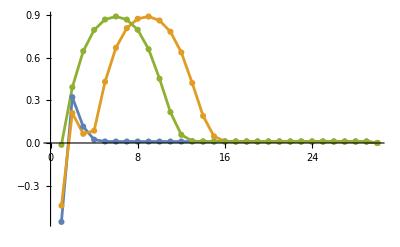

```mathematica
CPs=Import["Generalized_PSC1_Function89090317.tsv"];
ListPlot[CPs,Joined->True,Mesh->All,
PlotRange->All]
```

```mathematica
CPs=Import["Full_Hessian_FH3_Function3765054.tsv"];
ListPlot[CPs,Joined->True,Mesh->All,
PlotRange->All]
```

```mathematica
CPs=Import["NONDQUAR_Function_(CUTE)31971351.tsv"];
ListPlot[CPs,Joined->True,Mesh->All,
PlotRange->All]
```

## CP Hunt: FindMinimum

OK.  I am going to set the hounds lose with n=30 on the faster problems.  I have a bunch of reps with s=10^4 trials in each on all the faster problems.  Each sweep should take about an hour.  It is 10am Sunday.  I have time for quite a few sweeps before 8am Monday.

```mathematica
SetDirectory["C:\\Users\\AllanStruthers\\Desktop\\GitHub\\Spring2025Classes\\Spring-Classes-2025\\NumOpt\\ReferencesAndResources\\ExtHunt"]
FastRange=Complement[Range[Length[TestSet]],{1,8,24}];
runs=100;n=30; s=10^4;
DiffTol=10^-4;
ConvTol=10^-4;
Quiet[
Table[
AbsoluteTiming[
Do[
fStruc=TestSet⟦i⟧;
{fName,f,x0 }={fStruc["Name"],fStruc["Definition"],fStruc["x0"][n]};
ClearAll[df,ddf,CPs];
(* Something in the symbolic preprocessor chocked on the original function form *)
{g,df,ddf}=BuildGradAndHessAndFun[f,n];
CPs={};
Do[
(* Precision goal set down to encourage termination at saddles. *)
(* Required modification of the other tolerances *)
xx= Chop[Quiet[Quiet[x/.FindMinimum[g[x],{x,x0},PrecisionGoal->6]⟦2⟧]]];
If[Norm[df[xx]]<ConvTol,CPs=SortSplitKeep[CPs,xx,DiffTol]],
{s}];
FileName=StringReplace[StringJoin[fName,ToString[RandomInteger[10^8]],".tsv"]," "->"_"];
Export[FileName,CPs],
{i, FastRange}
]],
{runs}]]
```

C:\Users\AllanStruthers\Desktop\GitHub\Spring2025Classes\Spring-Classes-2025\NumOpt\ReferencesAndResources\ExtHunt

$Aborted

I made lots of different samples.  Lots of them will have repeats. I need to merge the matching data sets.  An empty data set does not import correctly.  It gives $Failed.  It is easy enough to merge all the matching file names.

```mathematica
i=2;
SetDirectory["C:\\Users\\AllanStruthers\\Desktop\\GitHub\\Spring2025Classes\\Spring-Classes-2025\\NumOpt\\ReferencesAndResources\\CPHunt"];
fname=StringReplace[StringJoin[TestSet⟦i⟧["Name"],"*.tsv"]," "->"_"];
Files=FileNames[fname];
DiffTol=1.0 10^-10;
Data=DeleteCases[Map[Import,Files],$Failed];
MergedData={};
Do[
MergedData=Split[Sort[Join[MergedData,Data⟦i⟧]],Norm[#1-#2]<DiffTol&]⟦All,1⟧,
{i, Length[Data]}];
MergedData
```

{{-0.555376,0.322445,0.115178,0.0235062,0.0106614,0.010218,0.0102086,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102083,0.0102042,0.0100041,0.000100082}}

```mathematica
CPs=Import["Generalized_Rosenbrock_Function4850561.tsv"];
ListPlot[CPs,Joined->True,Mesh->All]
```

Did I just find another Gen Rosen starting from zero!
{-0.0129151,0.392312,0.645951,0.795379,0.869043,0.890503,0.868331,0.796619,0.660077,0.452424,0.217116,0.0577326,0.0134706,0.0102865,0.01021,0.0102085,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102084,0.0102083,0.0102042,0.0100041,0.000100082}

-Graphics-

```mathematica
CPs=Import["Generalized_PSC1_Function89090317.tsv"];
ListPlot[CPs,Joined->True,Mesh->All,
PlotRange->All]
```

```mathematica
CPs=Import["Full_Hessian_FH3_Function3765054.tsv"];
ListPlot[CPs,Joined->True,Mesh->All,
PlotRange->All]
```

```mathematica
CPs=Import["NONDQUAR_Function_(CUTE)31971351.tsv"];
ListPlot[CPs,Joined->True,Mesh->All,
PlotRange->All]
```

## Break

```mathematica
Map[Sort[Eigenvalues[ddf[#]]]&,StartPoints]
```

```mathematica
Hmm=Map[ddf,StartPoints]
Map[Dimensions,Hmm]
```

{{{6114.,-960.,0,0},{-960.,4042.,-800.,0},{0,-800.,6314.,-960.},{0,0,-960.,200.}},{{{27.3539,892.415,8171.73,8143.61},{-132.425,266.377,975.694,-1047.81},0,0},{{-132.425,266.377,975.694,-1047.81},{662.354,607.073,8047.31,-893.995},{-106.169,358.241,1029.89,-92.7514},0},{0,{-106.169,358.241,1029.89,-92.7514},{2216.73,2108.3,-174.853,9749.46},{375.814,-557.453,-109.747,-1160.52}},{0,0,{375.814,-557.453,-109.747,-1160.52},200.}}}

{{4,4},{4,4}}

```mathematica
x0=TestSet⟦i⟧["Name"]
f=fStruc["Definition"];
StartPoints=SamplesFromBox[x0,s];
```

<|Name→Generalized Rosenbrock Function,Definition→Function[x,Module[{n=Length[x],c=100.},∑_i^(n-1) (c (x⟦i+1⟧-x⟦i⟧^2)^2+(1.-x⟦i⟧)^2)]],x0→Function[n,Table[If[OddQ[i],-1.2,1],{i,n}]]|>

Function[x,Module[{n=Length[x],c=100.},∑_i^(n-1) (c (x⟦i+1⟧-x⟦i⟧^2)^2+(1.-x⟦i⟧)^2)]]

Generalized Rosenbrock Function

```mathematica
{df,ddf}=BuildGradAndHess[f,n];
x0=fStr
```

<|Name→Generalized Rosenbrock Function,Definition→Function[x,Module[{n=Length[x],c=100.},∑_i^(n-1) (c (x⟦i+1⟧-x⟦i⟧^2)^2+(1.-x⟦i⟧)^2)]],x0→Function[n,Table[If[OddQ[i],-1.2,1],{i,n}]]|>

Missing[KeyAbsent,X0][30]

fStr

```mathematica
AnalyzeSamplePoints[f_, x0_, s_Integer] := Module[
	{n, vars, gradFunc, hessFunc, scale, samples, sampledEvals, tallyIndices, findMinimum},
	n = Length[x0];
	(* Generate samples around the initial point x0, return scale vector*)
	{scale, samples} = SamplesFromBox[x0, s];

	(* Build gradient and Hessian functions *)
	{gradFunc, hessFunc} = BuildGradAndHess[f, n];
	
	(* Compute eigenvalues of the Hessian at each sample *)
	sampledEvals = Table[
		(* sometimes we get symbolic results *)
		N[Eigenvalues[hessFunc[samples[[i]]]]], {i, 1, s}
	];
	
	(* Classify the eigenvalues sign at each sample *)
	IndexEvals[λs_] := Module[
		{Indicator = Sign[λs]},
		{Count[Indicator, 1], Count[Indicator, 0], Count[Indicator, -1]}
	];
	
	(* Tally the number of positive, zero, and negative eigenvalues *)
	tallyIndices = Sort[
		Tally[Map[IndexEvals, sampledEvals]]
	];
	
	(* Run FindMinimum on the function f starting at x0 *)
(*	findMinimum = Quiet[
		FindMinimum[
			f[vars], 
			Evaluate[Thread[{vars, x0}]]
		]
	];*)
	
	(* Return results including the FindMinimum output *)
	<|
		"TallyIndices" -> tallyIndices,
		"SampledEvals" -> sampledEvals,
(*		"FindMinimum" ->  findMinimum,*)
		"ScaleVector" -> scale
	|>
];
```

## Testing

```mathematica
(*Define dimension and number of samples*)
n=10;
s=100;

(* Define the analysis routine *)
AnalyzeFunction[testFunction_, n_, s_] := Module[
{x0, f},
x0 = testFunction["x0"][n];
f = testFunction["Definition"];
result = AnalyzeSamplePoints[f, x0, s];
<|"Name" -> testFunction["Name"],
"AnalysisResult" -> result|>
];
```

```mathematica
fNames=Map[#["Name"]&,TestSet];
i=2;
{n,s}={32,100};
AnalyzeFunction[TestSet⟦i⟧,n,s]["AnalysisResult"]
```

<|TallyIndices→{{{24,0,8},4},{{25,0,7},3},{{26,0,6},8},{{27,0,5},20},{{28,0,4},18},{{29,0,3},33},{{30,0,2},10},{{31,0,1},3},{{32,0,0},1}},SampledEvals→{{15814.1,12393.9,11695.3,10950.3,9915.69,8754.6,8665.88,8498.02,7450.2,7276.84,7155.1,6791.1,5708.08,5592.82,5563.92,5105.37,4925.82,4290.3,4101.14,2832.13,2180.71,2167.2,1536.67,1447.75,1328.21,897.019,828.538,-288.034,-273.166,72.6481,-54.9062,9.43114},{12300.2,8543.78,8510.76,7061.04,6516.23,5024.57,3577.23,3404.28,2908.81,2733.11,2522.12,2432.22,2175.13,1733.95,1490.77,1472.56,1400.43,1381.46,1251.84,834.936,-684.487,-626.657,585.92,568.186,547.723,517.177,391.501,285.343,-244.389,194.959,-32.7663,9.44994},{14686.3,13047.5,11363.4,10395.7,10009.6,9215.33,8569.73,6952.92,6895.42,6691.39,5942.65,5474.37,5172.22,4407.29,3293.02,2418.66,2381.99,2147.66,1878.75,1803.4,1735.46,1560.4,936.933,848.616,-742.953,657.5,480.019,454.694,-352.903,-174.455,70.2901,11.0611},{10779.9,9877.17,7415.27,5962.99,5841.39,4148.03,3400.83,3080.73,2616.39,2303.04,2086.5,2057.03,1553.94,1522.58,1249.74,1085.2,850.46,820.747,743.136,649.454,593.754,-466.821,449.339,345.164,338.333,300.803,-236.975,-140.636,-94.4719,87.1315,30.6547,-19.4993},{13177.,9156.2,8896.01,8186.48,6865.62,6273.36,6228.74,5911.32,5312.64,3874.89,3569.92,3522.19,3442.24,2830.73,1954.56,1920.45,1878.45,1714.23,1411.36,1001.7,916.885,840.38,724.613,-675.62,646.021,-614.75,-608.465,439.316,-363.552,-318.428,137.29,14.5652},{13605.,11196.7,10561.2,10484.8,8480.79,6787.58,5810.75,5716.99,4259.54,3771.67,3122.06,2988.08,2794.62,2770.68,2591.15,2262.53,1573.33,1415.75,1196.52,1004.08,816.394,600.802,-515.489,464.659,387.978,-367.528,-337.248,253.184,229.79,-131.004,-56.0909,19.9884},{11899.4,10184.9,9889.26,9476.55,7191.05,6568.75,6347.01,5184.14,4816.43,4811.02,4547.42,3965.09,3751.13,3187.55,2419.17,2189.13,2133.78,2058.21,1602.03,1451.65,947.863,837.06,-633.924,-608.036,561.935,544.071,-497.855,-437.411,-365.465,227.955,-218.721,44.159},{15888.8,15662.2,11104.5,10776.,9393.54,8654.22,8535.63,7435.84,6763.08,2659.87,2400.27,2133.02,1870.96,1664.73,1639.71,1232.46,1047.57,899.742,756.539,729.089,-715.209,642.201,575.387,445.972,-303.003,-284.493,-255.864,118.446,117.317,115.878,81.5778,-51.284},{14675.3,13560.,11149.9,9599.9,8863.,8407.18,6370.23,6237.31,5475.02,4209.67,3940.39,3664.91,2987.68,2953.98,2596.66,2459.69,2112.74,1986.3,1088.17,990.291,-799.272,-770.859,699.713,-608.665,546.983,412.756,379.514,-356.343,178.255,111.871,-80.4092,77.1494},{10822.7,9745.38,9078.48,7551.36,7515.66,7116.77,6791.06,6036.39,5495.31,4585.15,4256.96,4072.23,3730.45,1810.46,1746.99,1547.06,1293.81,1025.61,889.713,772.329,634.695,610.485,554.167,-539.939,501.414,-322.154,260.207,-258.237,-216.995,85.4049,-49.4192,28.7564},{12667.6,11383.5,10158.5,10119.7,9185.83,9076.24,8922.16,7743.43,6870.57,5939.96,5405.48,4821.29,3923.54,3200.12,2294.12,2241.68,2230.63,1961.02,1629.29,1484.74,1209.37,988.502,976.626,483.213,-439.626,362.816,340.601,296.144,-288.065,96.3008,81.9924,-13.4737},{14733.7,13027.3,12234.8,9847.93,7759.14,5970.87,5120.57,5094.23,5004.05,4351.92,4157.97,4084.61,3197.11,3195.13,2937.15,2521.64,2284.28,2178.46,1928.59,1440.29,1217.16,1140.4,1103.93,-953.721,853.211,826.444,-686.252,-287.873,-251.718,202.223,200.963,-166.298},{12755.9,12555.7,11388.5,10285.,8621.18,7429.54,7108.94,6023.9,5873.47,4313.82,4260.65,3666.89,3314.15,2154.75,1664.85,1626.41,1575.5,1415.59,1317.34,1301.22,919.255,785.651,658.278,-557.739,503.557,449.095,-396.047,-284.188,238.574,171.314,72.3864,48.9263},{15634.6,11439.1,10196.,9294.3,8867.64,6789.15,6064.09,5794.34,5721.13,4969.12,3630.11,3477.48,2870.25,2868.54,1912.31,1450.23,1317.06,1203.78,929.029,928.03,-853.84,-629.163,453.507,416.478,-406.033,260.554,254.266,-136.652,106.402,-84.7116,49.1643,37.3708},{14347.2,8772.54,8752.21,7823.89,7716.99,7689.7,6183.37,5954.6,4599.48,4567.03,4278.62,4119.01,2872.43,2868.08,2383.69,2283.25,2163.26,2015.81,1652.55,1536.88,1516.72,1437.08,1152.99,-860.223,747.416,-721.153,635.136,-609.128,-349.887,336.739,-311.462,309.023},{14688.5,14249.6,12414.1,9011.75,8476.15,7816.3,6724.74,6572.61,6187.19,5380.05,4901.67,4026.37,3197.12,2677.43,2444.28,2302.05,1587.3,1370.59,1351.04,1079.9,1064.73,970.584,738.992,-429.048,377.597,323.12,288.511,259.514,77.735,59.3499,26.4699,-23.646},{14723.4,9670.13,8906.65,8109.32,6614.92,6249.84,5028.47,4629.79,4559.02,3611.64,2927.86,2871.33,1702.11,1578.49,1496.04,1350.88,952.445,831.883,802.905,-681.444,460.212,390.794,-357.501,-250.826,-236.322,215.962,-126.139,83.7583,70.1607,-53.9692,-24.8732,20.3331},{14369.6,14029.,13547.7,13136.,12158.2,11089.3,10237.3,7144.31,6817.36,6451.33,4904.4,3814.41,3679.51,2726.19,2678.94,2478.69,2316.23,1799.12,1714.26,1650.53,1128.91,1042.42,761.735,652.002,579.571,-544.595,466.047,449.299,279.831,34.7007,-20.0683,1.70021},{12117.6,11487.1,10281.,9895.95,9054.27,8837.93,8762.49,8343.35,6542.46,6322.95,5209.01,3461.13,3017.24,2082.37,2057.,2030.99,1494.61,1407.53,1227.25,1102.09,1005.13,947.083,942.761,-823.105,633.049,-354.578,348.263,-166.992,-164.782,-145.459,118.464,69.5722},{10235.5,9857.67,8876.62,8474.53,8256.02,7938.16,6555.76,6283.47,6177.9,6145.82,5335.01,5113.32,4410.15,3212.86,3139.69,1787.86,1292.51,1075.16,1057.2,955.396,764.462,-736.223,-643.659,640.343,-507.033,482.514,416.941,328.02,200.616,190.693,177.002,130.103},{12778.3,11898.3,9307.33,7878.51,6329.51,5476.7,4309.37,3601.43,3185.42,2679.71,2441.42,2318.67,1810.65,1646.09,1477.67,1188.99,1024.36,973.529,706.705,596.206,-494.084,464.12,-447.57,400.787,345.667,-335.577,272.908,164.249,65.651,57.8232,43.4652,-19.1958},{10901.9,10795.6,9735.1,9021.89,8991.79,8601.18,7448.17,6750.01,5691.43,3971.04,2739.57,2705.17,1906.35,1829.71,1543.46,1541.16,1303.66,1278.77,1221.4,1143.86,919.991,-711.774,702.254,698.195,398.004,392.972,348.116,340.203,336.179,-324.278,-159.538,-38.7246},{13999.9,12738.6,10883.4,8580.7,8316.33,7891.7,7692.87,6588.03,6236.53,6131.96,5686.77,5460.2,5167.87,3747.5,3540.97,3122.25,2964.,2398.87,1539.71,1365.12,1249.92,1168.96,1116.27,836.984,635.757,488.526,-325.238,-324.322,-201.636,108.673,62.9107,58.7433},{14896.6,13630.2,12698.7,12508.4,11984.8,10001.2,7559.55,6898.85,6634.34,5585.14,4577.96,4576.09,3714.03,3629.2,3468.53,3142.06,2743.87,2099.91,1503.9,1122.46,770.854,-625.176,613.257,-606.183,497.782,394.242,-235.48,-231.162,170.241,143.156,122.671,11.5652},{11283.,9558.14,7869.58,7474.14,5980.66,5864.31,5493.19,3978.12,3765.3,3559.33,3426.38,2966.16,2476.51,2188.86,2184.66,2172.91,2002.46,1960.31,1771.82,1467.96,1284.74,847.046,749.834,596.221,297.38,264.746,-232.141,-155.123,-106.688,-59.8583,26.2894,21.5835},{12450.3,9940.21,9455.82,7226.,4962.22,4399.47,4336.51,3347.82,3271.99,3029.9,2589.14,1523.29,1500.5,1428.17,1379.68,1297.47,1054.53,848.322,838.667,695.478,-579.12,567.64,498.464,442.263,338.825,269.813,189.154,167.6,-102.256,81.9944,53.4043,11.4327},{14349.7,13410.8,10798.7,10153.7,8359.94,6625.93,6100.3,6015.41,5436.92,4626.07,4480.72,3802.29,3429.15,3018.53,2950.86,2651.47,2339.29,1754.71,1548.07,1525.43,1391.25,1307.64,1133.06,1025.63,832.056,731.153,668.316,-646.548,-458.,-352.773,66.0305,-28.7663},{13909.7,12759.4,10896.7,10030.2,9007.49,8723.41,7563.25,7340.27,6793.83,5923.59,5836.22,5115.42,5021.13,4940.66,4540.29,3488.08,2294.44,2158.73,2089.33,1736.96,1532.97,1339.03,1283.75,-925.204,-873.14,533.256,524.736,-381.151,-251.956,61.2254,57.8764,-11.8927},{13707.8,13363.8,10847.4,9903.7,8807.32,7531.45,5071.87,4011.91,2360.27,1706.23,1640.19,1322.32,1227.76,1062.15,996.309,860.328,807.233,796.651,728.704,632.043,-611.248,512.089,460.496,-431.925,413.738,403.059,292.046,263.556,231.986,103.065,77.5144,-43.7249},{11471.3,10330.6,10006.4,8193.33,7616.73,6012.15,5604.09,5223.81,4982.39,4453.15,4242.59,4071.12,3278.34,2137.86,1554.12,1428.19,1254.09,1246.36,1192.72,1097.71,949.975,699.23,647.807,-383.651,372.5,336.755,304.285,-164.053,149.172,143.843,-125.513,69.3104},{10898.6,10831.6,10789.9,10591.,9309.74,6113.68,5890.51,4944.76,4898.18,3856.9,2998.05,2765.84,2353.32,1635.49,1535.6,1523.45,1300.25,1127.17,-964.843,908.159,843.704,718.096,-618.411,551.252,516.884,477.666,453.028,379.64,153.292,150.124,-136.626,61.9576},{12733.3,12303.8,9672.5,8904.41,7713.17,6688.46,5624.19,4064.33,3340.46,3323.03,3204.93,1977.57,1460.59,1267.57,1261.29,980.933,-973.732,748.968,659.636,534.,-513.92,-493.412,465.868,395.191,340.066,249.434,198.71,-141.74,-138.952,101.795,83.432,-1.7154},{9980.72,9405.54,8621.42,7990.99,7252.9,5792.57,4738.9,4694.47,4650.88,4600.42,4508.,3714.56,2782.72,2557.,1890.96,1686.27,1679.08,1634.04,1572.62,1055.82,1049.69,989.862,-889.834,888.472,810.242,550.906,-239.965,-237.416,124.385,-93.6639,-86.4514,52.7706},{10056.5,9287.79,7776.33,7743.87,7418.05,5115.03,4764.04,3904.12,3397.25,3370.31,2743.75,2266.07,2194.14,1723.17,1683.95,1670.35,1292.7,1285.34,1276.,1033.7,-893.02,876.234,682.714,472.014,425.787,367.252,256.913,216.928,186.081,-167.952,-72.7982,-58.5048},{14841.5,14566.,13833.7,11848.1,9152.59,8605.52,7482.18,6796.04,6225.51,4928.67,4879.17,3002.1,2921.53,2613.75,2285.31,1880.27,1877.26,1744.87,1567.78,1413.81,1336.5,1298.08,1115.37,1114.34,1078.73,991.502,796.183,604.641,-354.702,311.718,-139.263,127.689},{14586.5,14391.4,9404.11,8807.83,6632.99,6574.64,6208.8,4685.55,4562.73,4174.1,3613.26,2785.2,2275.19,2065.52,1984.57,1894.13,1814.44,1565.31,1326.62,1313.47,1104.01,905.25,898.302,550.917,403.411,234.941,228.774,173.547,-120.916,110.246,-100.227,-51.6122},{15490.9,13207.8,13184.4,12647.4,11468.5,9086.83,8315.37,8068.16,7433.88,7404.95,6748.24,6624.15,4881.62,4271.49,4175.16,4081.98,3715.18,2911.9,2657.98,2456.32,2111.17,1575.47,1565.02,1151.1,1080.94,-818.607,-626.476,618.471,569.244,397.399,-309.588,69.2419},{8388.54,8166.31,7289.76,6299.,5271.21,4981.25,4675.21,4511.09,3979.01,3874.92,3394.11,1935.66,1768.75,1756.83,1260.48,1253.24,1123.2,892.649,823.779,760.982,650.859,567.65,469.046,-449.523,413.961,-267.011,217.497,-147.065,138.172,110.43,99.7678,37.4175},{12834.1,10844.4,8492.74,8221.03,6710.59,5004.4,4761.44,4335.03,3695.49,2854.52,2466.01,2341.06,2163.28,2094.14,1979.15,1736.15,1477.04,1345.36,1330.18,1113.16,-943.206,729.668,694.925,639.799,544.611,256.877,171.483,158.457,-152.343,-133.999,-90.483,-35.3019},{14700.7,14378.1,7583.76,6093.04,5932.36,5462.94,5263.34,4570.48,3954.18,3618.14,3442.3,2326.22,2126.42,1998.47,1939.02,1702.94,1384.96,1301.93,1280.3,1083.83,948.412,945.172,864.025,826.749,775.472,676.256,642.461,618.163,596.055,155.04,115.608,58.4322},{14383.4,13149.9,12298.6,11330.6,9734.81,6696.91,6419.38,5533.94,5511.41,5039.79,3548.62,2591.71,2529.24,2401.43,2309.23,2249.28,1938.18,1231.43,994.166,951.742,888.076,861.654,-677.008,634.044,-549.524,-540.735,526.89,444.202,305.407,200.124,104.61,20.7248},{11629.3,11060.7,10391.5,10000.7,8748.29,7672.68,7604.9,7466.37,6595.03,6211.57,5517.37,4807.87,4686.8,3234.69,3049.99,2513.27,2111.92,2024.83,1785.13,1604.22,1472.94,1185.61,900.27,837.064,621.3,-510.347,436.514,393.134,321.913,-138.264,104.176,-42.2497},{13874.2,10445.,8812.06,7872.01,6164.33,4250.98,3860.59,3829.02,3357.87,3356.46,2332.46,1787.14,1731.19,1590.94,1194.72,871.678,807.307,730.493,729.729,727.964,667.259,-640.568,407.106,394.616,-358.947,-335.177,260.803,-216.742,155.404,-83.5733,-49.3611,-0.98587},{14453.3,13384.4,13261.2,13136.8,10881.5,9824.43,8668.94,8517.57,7199.03,6265.89,5444.87,3253.53,3034.25,2976.12,2860.57,2452.68,1752.06,1555.5,1255.93,1054.66,778.614,768.996,439.729,437.565,430.715,286.91,-285.24,-227.528,-207.331,157.933,35.8105,-30.7205},{13385.2,10704.5,7092.58,6559.16,5650.61,5512.71,5503.46,4731.88,3632.16,3035.96,2825.52,2362.14,2236.9,1615.38,1487.7,963.33,934.892,715.148,-621.319,-612.891,546.336,445.466,-406.964,391.371,389.077,-364.32,324.27,265.73,73.7183,-66.2022,58.17,-34.893},{14569.8,13217.6,10870.3,10556.8,8803.38,5919.96,5847.93,4643.19,4476.65,2810.56,2638.11,2571.04,1734.55,1474.45,1437.62,1424.13,1406.08,1376.39,1282.64,945.832,866.157,537.851,-392.141,376.374,-284.182,-255.41,-160.873,158.692,-126.201,111.604,88.9712,-25.4135},{13671.4,12396.1,10469.2,9594.19,8957.72,8737.26,7554.9,7486.39,6535.17,5579.65,4278.54,3687.39,3397.38,2968.6,2889.3,2000.51,1908.83,1763.42,1625.11,1383.13,1334.81,1109.64,957.038,897.986,711.345,681.804,666.254,458.713,-430.986,-409.222,71.5376,-15.7078},{14295.2,11565.7,9954.43,9020.54,8945.16,8103.53,7704.62,6258.74,6185.88,5878.05,5321.33,4894.5,4601.24,3470.33,3059.35,2740.01,2455.39,2449.93,2434.33,2340.18,1824.94,1552.31,1196.44,629.152,483.948,259.007,-225.518,-167.151,154.045,-150.713,-95.3191,55.889},{14151.5,12299.7,10904.5,10608.5,9397.6,8704.19,7396.35,6376.7,5553.25,4130.75,3730.39,3294.84,3001.33,2204.95,2201.04,1494.06,1483.38,1425.57,1379.48,1320.86,1181.74,898.507,810.283,736.78,-497.525,-493.857,431.054,351.88,270.702,202.61,71.4803,-47.8266},{12752.,11728.7,11228.1,9836.66,8791.21,8747.11,8690.27,6734.23,6285.69,4292.23,3507.04,2053.65,1931.88,1630.28,1480.37,1280.41,1161.08,811.244,789.081,-780.697,716.025,-653.357,623.776,535.838,402.132,388.846,226.374,188.136,85.9096,33.046,15.9205,-9.40258},{8557.74,8193.51,6615.86,6568.1,6238.6,5873.03,5120.42,5075.67,4480.66,4159.74,3296.47,3093.91,2424.8,2195.11,2180.64,1844.85,1624.64,1554.63,1356.44,1044.17,714.544,-545.101,476.818,377.316,-376.776,356.905,269.947,-185.715,106.717,74.1935,61.4146,44.4335},{15065.4,12223.1,8517.5,8059.24,7510.59,6769.42,6724.59,5547.52,5178.52,4883.3,4299.96,3143.22,2915.23,2154.87,2072.13,2021.49,1736.22,1523.36,1169.18,994.178,980.38,962.845,620.932,600.583,468.515,415.255,391.613,333.514,306.308,137.613,-120.807,67.737},{13552.4,13509.3,11629.2,10153.3,6799.44,5248.44,4959.36,4590.3,4094.86,3676.67,3514.87,3110.29,2332.66,1861.06,1854.56,1639.98,1515.93,1219.22,923.907,898.851,834.768,768.028,659.493,-533.821,434.373,-397.5,360.628,-358.294,283.047,174.114,-111.755,90.3833},{13100.6,11278.2,10037.6,9900.07,3688.48,3661.45,3636.99,3508.85,2749.04,2335.24,1848.96,1758.64,1420.97,1335.3,1301.75,-1015.5,864.55,863.224,777.979,-529.4,-438.513,-406.348,385.984,356.404,-340.657,-315.266,216.359,201.23,-195.857,152.849,-62.9459,12.2324},{10808.4,10695.,8814.17,7198.21,6405.08,4819.06,4520.3,4228.87,3586.9,3027.05,2487.58,2432.64,2356.72,1813.38,1698.96,1560.39,1483.96,1340.76,1043.27,1005.44,924.117,882.59,847.692,740.892,600.544,-474.03,437.386,149.284,-90.5465,65.0743,-57.258,-24.4711},{8008.49,7365.27,6219.84,5832.04,5700.,5348.87,5305.46,5220.93,5012.44,3908.23,3694.86,2115.17,2076.72,2042.95,1530.32,1473.15,1159.14,1135.44,955.026,615.711,509.857,365.176,257.71,-255.36,-207.06,-159.413,154.573,129.855,-98.6617,-34.7423,34.0565,-12.6709},{11651.4,9636.61,8263.64,7761.11,7682.76,6998.01,4762.91,4487.25,4076.16,4033.05,3441.44,2851.14,2784.09,2643.29,2284.33,2265.06,1936.31,1701.12,1470.89,1111.84,1085.52,1042.86,1023.44,-906.94,789.864,452.475,429.687,-351.191,298.19,-237.964,-176.858,66.9916},{13684.3,12568.3,10682.7,9653.98,8918.87,8846.29,8173.13,6111.57,4052.18,3917.45,2306.77,1953.62,1871.69,1793.98,1360.9,1323.5,1230.79,-961.681,-902.4,848.507,736.332,-674.8,-608.004,556.951,471.905,460.934,333.472,246.252,226.265,-90.4256,56.8349,-42.984},{14788.3,13373.5,11900.,9261.37,8912.5,8468.59,8209.43,7668.44,7472.,6495.96,6340.76,6030.77,5827.38,4627.18,3258.45,1995.52,1712.38,1146.12,1075.53,775.087,665.063,654.912,651.242,-585.065,-509.181,476.434,193.242,-155.934,127.024,83.4683,57.0493,12.1386},{14772.7,13344.6,9046.22,8184.07,6742.32,4289.1,3966.08,3641.43,3272.72,2754.78,2366.11,2361.22,2304.05,2150.27,1840.24,1666.42,1651.69,1614.86,1517.56,1292.71,1144.21,974.159,756.936,684.832,634.359,544.282,401.393,-320.633,-294.819,246.244,208.598,136.883},{14440.5,11594.,10491.9,10453.1,8769.34,7620.51,6955.95,6953.02,4571.18,4189.77,3788.67,3248.77,3224.09,2083.74,1885.35,1746.48,1634.64,1360.76,1248.07,1036.77,-971.502,949.714,636.775,-559.387,506.968,-465.951,-410.207,355.485,-225.89,200.478,-166.729,-81.1606},{15656.4,14018.,13057.9,11210.6,11139.3,8442.03,7733.54,7042.4,6462.68,6113.87,5610.59,5233.78,5210.13,4247.41,3843.15,3282.92,3200.91,2227.49,2206.07,2130.9,2087.08,1991.87,1984.53,1548.66,1368.,960.026,867.586,774.33,662.468,-353.366,69.3828,66.6611},{15265.3,14827.7,11100.1,9912.35,9282.56,8293.91,5525.01,5413.45,4874.11,4212.14,3900.23,3424.53,3223.78,2753.65,2211.34,1723.42,1343.83,1282.69,1008.12,-708.14,689.985,644.438,-609.519,535.018,-531.204,477.1,-439.196,330.2,283.352,187.591,74.5985,-69.2333},{13809.7,11488.,10193.3,8780.45,6793.82,5890.35,5137.03,5128.62,4375.74,3503.02,3455.74,2778.07,1996.85,1950.75,1625.6,1588.99,1375.89,1343.41,1063.09,990.907,922.515,-835.517,792.49,640.438,455.44,-227.991,-220.763,219.114,-214.053,128.046,79.8095,-15.6073},{13424.4,13139.,12653.2,12185.5,12051.5,11565.3,10975.1,10723.8,9205.75,9098.28,8568.65,8459.52,6376.76,4250.32,4013.94,2824.13,2772.42,2602.41,2173.04,2028.82,1803.67,1448.89,1412.95,1357.1,1159.08,-842.348,691.092,-608.173,566.184,369.213,200.332,92.0134},{12977.,11307.7,8978.83,7954.73,7349.06,6822.5,5606.05,4372.64,3932.46,3870.04,3237.15,3068.57,2907.52,2667.89,2071.89,1815.5,1579.4,1325.4,1260.39,1067.39,919.434,-835.878,785.455,744.746,726.865,-592.074,-571.844,-456.925,369.458,237.446,152.859,62.9914},{12575.6,12251.3,11813.2,10748.3,9582.5,9578.69,9436.89,6314.67,3467.43,3433.77,2920.51,2870.31,2713.79,2445.24,2388.61,1904.48,1809.54,1366.88,1358.42,1334.26,1080.79,1048.08,-870.498,843.775,715.432,418.799,-275.556,259.96,258.734,161.817,61.7892,52.7129},{15708.6,13983.7,11565.8,9972.98,8583.16,7225.24,6744.67,5660.37,5446.13,4389.94,4369.6,4181.98,4006.83,3183.1,2221.43,2141.52,1901.73,1732.42,1560.74,1250.34,844.662,662.064,588.461,-555.487,517.603,411.33,-257.346,255.792,235.584,-167.201,131.537,-109.962},{14385.,12368.,12335.,11990.6,10508.9,10499.9,10296.6,8264.74,6953.67,6735.13,5446.52,3479.55,3312.55,3056.17,2557.23,2511.67,2034.63,1983.77,1463.04,1357.4,1214.33,948.29,753.382,562.407,550.241,423.823,308.557,307.083,-268.894,215.421,-184.185,-122.07},{12530.7,10857.2,8944.88,6869.16,5825.59,5730.2,3561.88,2851.68,1997.46,1945.11,1765.04,1743.3,1605.93,1520.75,1209.16,1150.45,1051.18,764.481,712.037,650.702,-563.212,446.593,410.275,386.743,-278.196,-216.54,210.555,206.846,-181.579,171.261,99.422,-91.2137},{9135.67,8685.,8428.16,6201.44,4210.44,3990.54,3843.81,2812.88,2191.77,2180.26,2123.47,2104.12,1790.15,1602.98,1248.78,1233.93,1212.6,1134.27,1051.92,1012.2,906.249,812.763,662.566,639.053,545.846,-384.957,353.43,-237.068,208.726,-145.487,-122.472,20.8536},{15223.2,14756.9,14518.,13860.2,11045.,10150.2,8860.64,8320.22,6612.61,4219.31,3049.57,2830.27,2786.22,2394.44,2295.44,1927.02,1807.53,1621.99,1447.37,1382.31,1356.84,1162.36,1079.41,795.751,637.304,628.43,364.827,250.934,176.47,-157.084,79.9589,-19.6132},{15144.4,11351.9,10851.6,10825.2,10519.6,7654.2,6886.6,6573.18,6033.26,5370.05,4044.78,3172.98,3003.7,2750.56,2498.73,1907.09,1767.,1344.05,971.244,967.382,-805.736,713.785,-641.579,626.681,-604.405,-582.761,518.252,449.987,367.909,-272.024,118.043,40.7698},{15123.1,13553.4,11148.5,10815.2,8823.97,8492.95,4965.06,3920.77,3600.16,3522.54,3150.15,3046.26,2947.34,2905.45,2715.34,2511.65,1812.26,1784.44,634.461,-609.539,544.462,508.751,492.107,449.691,417.701,302.621,286.851,-233.565,-154.755,-77.0295,-62.9395,58.4622},{10766.,9018.69,7741.02,7316.36,6182.94,5449.49,5250.92,4622.93,4027.76,3953.38,3254.96,3045.92,2969.26,2768.51,2621.68,1963.7,1831.49,1277.33,-860.264,710.014,-686.366,681.369,665.278,-574.722,-571.657,490.715,-425.975,-389.368,294.341,-292.715,-172.453,91.7056},{15800.4,15576.,12187.2,11614.3,10402.5,7584.16,7318.22,7313.74,7184.62,6439.74,5686.72,5625.73,2663.4,1801.74,1756.51,1383.48,1372.97,1315.22,1243.4,1210.21,1124.33,1008.27,-781.081,687.909,-609.826,512.868,447.852,424.217,124.842,119.585,-57.4108,57.2208},{11398.,9553.04,9534.94,8930.38,7406.25,6977.09,6587.58,6101.76,6094.78,5362.5,4978.52,4253.29,4241.92,4171.99,3488.86,3316.38,2751.86,1748.15,1602.59,1239.38,1184.9,-997.504,-669.353,637.108,-452.056,362.338,-220.873,185.429,89.0795,-47.9092,28.9985,-6.7801},{14762.6,10814.5,10456.4,10288.2,9809.11,8632.91,5941.64,5500.58,5245.78,5038.43,4760.7,4124.08,3740.33,3703.02,3452.65,1884.34,1458.15,1377.96,942.005,-802.239,742.354,713.637,549.586,426.197,-362.337,-343.944,295.952,241.657,228.308,106.297,87.1395,53.1335},{13959.1,13929.9,13819.4,12388.2,11602.7,10650.8,9976.18,8620.3,7835.03,7794.85,7786.54,7496.39,6538.55,5479.81,3820.94,3089.15,2359.76,2227.96,1740.78,1648.16,1349.36,921.806,701.023,619.185,576.283,479.171,395.694,-373.072,267.986,238.065,-48.4712,-5.66303},{15305.2,9484.16,7227.77,7024.08,6441.97,6376.75,5859.99,5134.78,4886.28,4813.75,3592.31,3585.47,2891.58,2242.8,2063.7,1845.36,1458.38,1265.33,1005.93,919.389,893.347,695.842,607.478,579.899,-496.865,-411.426,330.287,203.893,-143.386,132.763,103.143,-48.8675},{15484.1,14785.,12359.4,12123.,11859.,11590.1,8591.84,8352.06,7481.86,7470.44,6652.88,5241.65,5029.91,4859.31,2892.86,2391.11,2115.94,1903.05,1726.2,1689.,1663.18,1075.89,777.015,727.922,718.922,367.473,-348.278,339.551,-261.023,126.505,44.2176,-43.627},{15811.8,15137.5,14788.1,13769.7,13242.4,11372.1,11349.6,10565.2,9425.38,8777.9,8155.36,8128.61,5903.94,5470.52,5305.96,5135.8,4624.75,4159.97,3961.43,2035.52,1506.53,1447.04,1415.16,809.601,-722.76,685.994,624.239,-619.534,471.083,150.322,73.2207,-59.0966},{13744.6,13232.7,12831.8,7361.02,7078.68,6819.87,5453.57,4844.07,4362.35,3827.56,3496.07,2391.34,2194.4,2162.48,2117.96,1463.01,1328.3,1240.,1007.27,892.714,880.257,820.245,721.959,608.367,597.888,399.399,-374.158,-286.181,-257.44,238.894,120.412,99.1746},{14128.3,12297.3,9895.63,9776.33,9686.33,8650.8,6846.86,6396.45,6012.04,5609.91,5121.77,5046.28,4634.53,4176.72,3931.35,3639.1,3450.92,3187.12,2908.58,2766.49,2150.61,1177.87,1098.78,963.923,906.921,534.346,335.968,-183.654,86.9273,-76.5563,75.2682,-25.5563},{14942.1,10359.5,10105.9,7070.54,6959.26,6769.77,6284.35,6270.3,4771.81,3793.94,3588.4,2632.87,2259.47,2132.26,2070.91,1287.28,1280.79,966.673,833.12,-824.308,-795.951,723.406,611.465,-464.88,212.691,202.568,192.12,172.609,-148.457,63.9948,61.7223,37.876},{14505.4,14034.,13634.7,10101.7,8833.51,8633.39,7911.85,7787.68,7709.55,7359.91,6205.02,4670.94,3869.77,3841.66,3060.8,2641.56,2636.98,2255.44,1505.04,1181.13,1152.95,1078.23,1054.04,986.977,592.565,519.658,449.407,364.72,-356.325,-212.851,103.671,35.6666},{14671.2,14309.1,13455.3,11719.5,9421.79,9360.55,7943.33,6356.28,5636.09,5086.59,4354.14,4269.96,3804.16,3424.97,2845.74,2413.08,2061.64,1370.86,1305.33,986.365,-957.29,900.095,-859.255,778.489,461.876,414.353,338.511,228.02,187.327,-129.558,111.395,14.8765},{14270.1,10966.4,9985.31,8867.8,8225.99,8139.33,7814.07,7698.33,5403.62,5207.21,4967.8,4752.16,4097.04,3971.64,3283.27,2997.66,2008.04,1841.53,1167.08,1115.42,1058.13,1000.08,-953.855,-877.642,637.035,-619.147,516.887,375.423,192.06,142.282,68.8937,52.8747},{14860.6,14548.1,14235.8,11326.5,10979.7,10716.8,10237.1,7704.59,6899.79,5985.03,5291.27,5112.68,3753.91,2381.48,2227.19,2206.17,1849.97,1519.43,1513.34,1489.76,1080.98,874.294,789.161,719.926,-712.506,356.402,351.666,206.034,-198.663,-118.4,18.1815,9.81377},{13460.2,13351.1,12624.1,11502.7,10339.2,9642.03,9291.21,8314.,7722.54,5744.66,5100.49,4344.19,4133.7,3163.55,2832.78,2480.09,2312.3,2043.37,1895.54,1891.56,1721.86,1554.82,1459.73,890.422,643.6,-612.117,594.296,-457.567,-290.26,211.885,120.641,21.391},{15445.5,10394.8,9151.42,9030.87,8406.85,8081.1,6996.71,6074.83,5868.31,5141.72,4557.4,3421.66,3157.85,2728.12,2656.81,2301.2,1959.52,1790.33,1729.76,1349.94,1283.92,1042.21,1034.96,811.951,748.126,-679.188,648.395,-566.261,-431.659,371.41,200.002,42.483},{15762.5,11390.3,11181.9,8227.,8204.02,8180.84,7176.25,6258.02,5972.49,5654.6,5108.75,5102.19,3842.4,3298.48,2919.14,2916.04,2808.32,1886.34,1327.28,1090.92,991.049,-950.77,859.084,689.726,-476.446,397.869,-370.676,200.725,-160.162,-147.985,132.946,-91.8122},{10679.,9643.81,9525.92,8196.86,7988.28,7305.28,7089.11,6459.31,6365.52,6116.27,5857.67,5532.73,4678.56,4647.13,3238.13,2596.79,1975.09,1835.14,1668.97,1298.8,1207.66,845.256,841.207,558.827,471.421,-248.444,-151.745,114.782,-104.89,-81.6799,13.406,-6.60895},{14044.4,13561.,10330.6,6640.21,5802.95,5383.96,4733.12,4446.41,4398.03,4103.01,4075.31,3979.79,3805.3,3775.95,2716.34,2175.69,2174.01,1876.32,1842.81,1698.27,1415.08,1320.57,1287.84,1229.88,1013.62,869.005,841.001,668.532,552.686,-281.021,-224.655,-208.55},{14716.2,9558.7,8579.13,7965.1,7223.07,7036.32,5689.94,5403.8,4967.99,4769.67,2319.81,2227.81,2081.07,2022.62,1786.09,1504.27,1394.26,1190.37,1160.35,928.935,775.384,641.443,449.098,427.766,-345.049,-302.475,-282.211,-164.795,101.08,70.7598,47.7857,-9.82238},{14220.,11326.6,10482.,9981.12,7640.53,7322.98,6874.94,6271.01,4970.2,4794.35,4751.02,3877.85,3422.16,2504.78,2150.18,1943.66,1894.84,1651.55,1391.37,1338.07,1337.16,1299.11,1056.39,754.464,500.552,381.476,365.003,352.091,-333.03,66.8188,50.341,-44.1777},{12289.5,10216.,8284.96,7612.22,7592.58,7051.42,5489.51,3896.14,3168.44,2725.55,1759.56,1666.03,1592.,1380.47,1367.01,1177.93,1072.88,-870.258,802.413,708.09,586.969,586.711,-508.07,431.391,360.916,-298.073,286.658,201.198,138.733,79.9823,-37.2357,8.90196},{14215.5,13860.5,11852.8,10791.,10779.1,10583.6,8302.11,8122.6,7800.26,7245.76,5212.,4875.83,4077.99,3971.44,3910.26,2783.69,2532.48,2098.29,1691.65,1648.58,1638.53,1364.13,1244.29,864.323,838.268,617.71,495.874,461.675,-327.901,182.76,156.188,61.2179},{11977.6,9336.91,7150.05,7076.27,6080.45,4123.57,3982.78,3070.22,2185.54,1921.58,1747.79,1685.33,1656.66,1527.24,1231.88,-1081.2,967.965,944.196,865.084,656.299,654.666,605.653,-497.042,403.242,-287.852,-242.404,-229.706,-158.077,-137.804,89.4846,85.3664,-75.249},{14402.6,10725.4,10553.,9658.13,9184.46,7454.27,5797.14,3422.23,3298.58,2533.06,2298.53,1893.31,1834.7,1464.35,1300.54,1203.83,990.088,976.949,-697.477,677.093,-652.455,-493.749,433.735,349.723,-276.343,-154.316,-125.107,111.98,-88.8837,67.9949,7.85651,-1.01415}},ScaleVector→{2.4,2.,2.4,2.,2.4,2.,2.4,2.,2.4,2.,2.4,2.,2.4,2.,2.4,2.,2.4,2.,2.4,2.,2.4,2.,2.4,2.,2.4,2.,2.4,2.,2.4,2.,2.4,2.}|>

TestSt

```mathematica
AnalyzeFunction[]
```

```mathematica
resultsList=Map[AnalyzeFunction[#,n,s]&,TestSet];
TableForm[Table[resultsList[[i]]["AnalysisResult"]["TallyIndices"], {i, 1, 47}],
TableHeadings->Automatic]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 |  | 1 | 2 | 3
1 | 10 | 0 | 0
2 | 100 |  |  |  |  |  |  |  |  |  |  | 
2 | 1 | 7 | 0 | 3
2 | 10 |  |  | 8 | 0 | 2
19 |  |  | 9 | 0 | 1
46 |  |  | 10 | 0 | 0
25 |  |  |  |  |  |  |  | 
3 | 1 | 10 | 0 | 0
2 | 100 |  |  |  |  |  |  |  |  |  |  | 
4 | 1 | 10 | 0 | 0
2 | 100 |  |  |  |  |  |  |  |  |  |  | 
5 | 1 | 1 | 0 | 9
2 | 100 |  |  |  |  |  |  |  |  |  |  | 
6 | 1 | 7 | 0 | 3
2 | 8 |  |  | 8 | 0 | 2
29 |  |  | 9 | 0 | 1
42 |  |  | 10 | 0 | 0
21 |  |  |  |  |  |  |  | 
7 | 1 | 10 | 0 | 0
2 | 100 |  |  |  |  |  |  |  |  |  |  | 
8 | 1 | 10 | 0 | 0
2 | 100 |  |  |  |  |  |  |  |  |  |  | 
9 | 1 | 10 | 0 | 0
2 | 100 |  |  |  |  |  |  |  |  |  |  | 
10 | 1 | 10 | 0 | 0
2 | 100 |  |  |  |  |  |  |  |  |  |  | 
11 | 1 | 10 | 0 | 0
2 | 100 |  |  |  |  |  |  |  |  |  |  | 
12 | 1 | 4 | 0 | 6
2 | 2 |  |  | 5 | 0 | 5
7 |  |  | 6 | 0 | 4
25 |  |  | 7 | 0 | 3
36 |  |  | 8 | 0 | 2
23 |  |  | 9 | 0 | 1
6 |  |  | 10 | 0 | 0
1 |  |  |  |  | 
13 | 1 | 0 | 0 | 10
2 | 74 |  |  | 1 | 0 | 9
26 |  |  |  |  |  |  |  |  |  | 
14 | 1 | 1 | 0 | 9
2 | 2 |  |  | 2 | 0 | 8
4 |  |  | 3 | 0 | 7
17 |  |  | 4 | 0 | 6
31 |  |  | 5 | 0 | 5
20 |  |  | 6 | 0 | 4
18 |  |  | 7 | 0 | 3
6 |  |  | 8 | 0 | 2
2 |  |  |  | 
15 | 1 | 5 | 0 | 5
2 | 1 |  |  | 6 | 0 | 4
28 |  |  | 7 | 0 | 3
61 |  |  | 8 | 0 | 2
10 |  |  |  |  |  |  |  | 
16 | 1 | 10 | 0 | 0
2 | 100 |  |  |  |  |  |  |  |  |  |  | 
17 | 1 | 4 | 0 | 6
2 | 6 |  |  | 5 | 0 | 5
39 |  |  | 6 | 0 | 4
50 |  |  | 7 | 0 | 3
5 |  |  |  |  |  |  |  | 
18 | 1 | 7 | 0 | 3
2 | 1 |  |  | 8 | 0 | 2
46 |  |  | 9 | 0 | 1
42 |  |  | 10 | 0 | 0
11 |  |  |  |  |  |  |  | 
19 | 1 | 10 | 0 | 0
2 | 100 |  |  |  |  |  |  |  |  |  |  | 
20 | 1 | 10 | 0 | 0
2 | 100 |  |  |  |  |  |  |  |  |  |  | 
21 | 1 | 8 | 0 | 2
2 | 3 |  |  | 9 | 0 | 1
36 |  |  | 10 | 0 | 0
61 |  |  |  |  |  |  |  |  | 
22 | 1 | 10 | 0 | 0
2 | 100 |  |  |  |  |  |  |  |  |  |  | 
23 | 1 | 1 | 0 | 9
2 | 2 |  |  | 2 | 0 | 8
7 |  |  | 3 | 0 | 7
9 |  |  | 4 | 0 | 6
15 |  |  | 5 | 0 | 5
17 |  |  | 6 | 0 | 4
15 |  |  | 7 | 0 | 3
14 |  |  | 8 | 0 | 2
13 |  |  | 9 | 0 | 1
8 |  |  | 
24 | 1 | 10 | 0 | 0
2 | 100 |  |  |  |  |  |  |  |  |  |  | 
25 | 1 | 10 | 0 | 0
2 | 100 |  |  |  |  |  |  |  |  |  |  | 
26 | 1 | 5 | 0 | 5
2 | 1 |  |  | 6 | 0 | 4
18 |  |  | 7 | 0 | 3
31 |  |  | 8 | 0 | 2
33 |  |  | 9 | 0 | 1
14 |  |  | 10 | 0 | 0
3 |  |  |  |  |  | 
27 | 1 | 10 | 0 | 0
2 | 100 |  |  |  |  |  |  |  |  |  |  | 
28 | 1 | 10 | 0 | 0
2 | 100 |  |  |  |  |  |  |  |  |  |  | 
29 | 1 | 10 | 0 | 0
2 | 100 |  |  |  |  |  |  |  |  |  |  | 
30 | 1 | 10 | 0 | 0
2 | 100 |  |  |  |  |  |  |  |  |  |  | 
31 | 1 | 10 | 0 | 0
2 | 100 |  |  |  |  |  |  |  |  |  |  | 
32 | 1 | 0 | 0 | 10
2 | 1 |  |  | 1 | 0 | 9
3 |  |  | 2 | 0 | 8
15 |  |  | 3 | 0 | 7
22 |  |  | 4 | 0 | 6
27 |  |  | 5 | 0 | 5
13 |  |  | 6 | 0 | 4
9 |  |  | 7 | 0 | 3
4 |  |  | 8 | 0 | 2
5 |  |  | 9 | 0 | 1
1 |  | 
33 | 1 | 6 | 0 | 4
2 | 1 |  |  | 7 | 0 | 3
11 |  |  | 8 | 0 | 2
33 |  |  | 9 | 0 | 1
33 |  |  | 10 | 0 | 0
22 |  |  |  |  |  |  | 
34 | 1 | 5 | 0 | 5
2 | 100 |  |  |  |  |  |  |  |  |  |  | 
35 | 1 | 4 | 0 | 6
2 | 2 |  |  | 5 | 0 | 5
19 |  |  | 6 | 0 | 4
36 |  |  | 7 | 0 | 3
25 |  |  | 8 | 0 | 2
13 |  |  | 9 | 0 | 1
5 |  |  |  |  |  | 
36 | 1 | 10 | 0 | 0
2 | 100 |  |  |  |  |  |  |  |  |  |  | 
37 | 1 | 10 | 0 | 0
2 | 100 |  |  |  |  |  |  |  |  |  |  | 
38 | 1 | 6 | 0 | 4
2 | 4 |  |  | 7 | 0 | 3
34 |  |  | 8 | 0 | 2
46 |  |  | 9 | 0 | 1
15 |  |  | 10 | 0 | 0
1 |  |  |  |  |  |  | 
39 | 1 | 7 | 0 | 3
2 | 17 |  |  | 8 | 0 | 2
25 |  |  | 9 | 0 | 1
45 |  |  | 10 | 0 | 0
13 |  |  |  |  |  |  |  | 
40 | 1 | 3 | 0 | 7
2 | 4 |  |  | 4 | 0 | 6
6 |  |  | 5 | 0 | 5
19 |  |  | 6 | 0 | 4
31 |  |  | 7 | 0 | 3
19 |  |  | 8 | 0 | 2
15 |  |  | 9 | 0 | 1
6 |  |  |  |  | 
41 | 1 | 6 | 0 | 4
2 | 3 |  |  | 7 | 0 | 3
21 |  |  | 8 | 0 | 2
16 |  |  | 9 | 0 | 1
26 |  |  | 10 | 0 | 0
34 |  |  |  |  |  |  | 
42 | 1 | 10 | 0 | 0
2 | 100 |  |  |  |  |  |  |  |  |  |  | 
43 | 1 | 1 | 0 | 9
2 | 5 |  |  | 2 | 0 | 8
8 |  |  | 3 | 0 | 7
22 |  |  | 4 | 0 | 6
28 |  |  | 5 | 0 | 5
19 |  |  | 6 | 0 | 4
13 |  |  | 7 | 0 | 3
3 |  |  | 8 | 0 | 2
2 |  |  |  | 
44 | 1 | 2 | 0 | 8
2 | 1 |  |  | 3 | 0 | 7
3 |  |  | 4 | 0 | 6
7 |  |  | 5 | 0 | 5
11 |  |  | 6 | 0 | 4
25 |  |  | 7 | 0 | 3
35 |  |  | 8 | 0 | 2
9 |  |  | 9 | 0 | 1
7 |  |  | 10 | 0 | 0
2 |  |  | 
45 | 1 | 10 | 0 | 0
2 | 100 |  |  |  |  |  |  |  |  |  |  | 
46 | 1 | 9 | 0 | 1
2 | 4 |  |  | 10 | 0 | 0
96 |  |  |  |  |  |  |  |  |  | 
47 | 1 | 5 | 0 | 5
2 | 2 |  |  | 6 | 0 | 4
6 |  |  | 7 | 0 | 3
18 |  |  | 8 | 0 | 2
33 |  |  | 9 | 0 | 1
30 |  |  | 10 | 0 | 0
11 |  |  |  |  |  |